# HW3-1

## a) Give the index for the fixed point (0,0), x’ = y-x; y’ = x^2

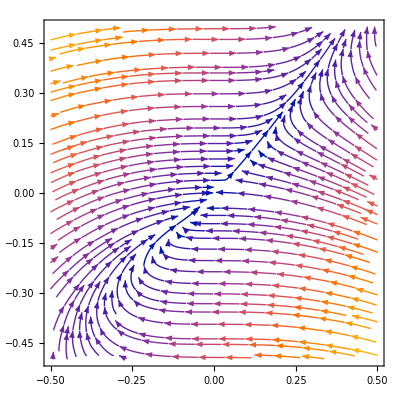

```mathematica
ClearAll["Global'.*"];
eq1 = y - x;
eq2 = x^2;

StreamPlot[{eq1, eq2}, {x, -0.5, 0.5}, {y, -0.5, 0.5}, StreamPoints -> Fine]
```

## b)-Graphics-

Polar to Cartesian:
-Graphics-

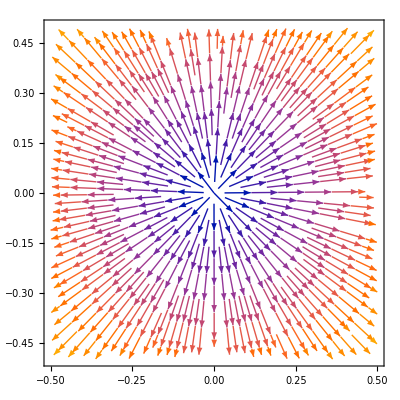

```mathematica
ClearAll["Global'.*"];
a = 1;
eq1 = a*x;
eq2 = a*y;

StreamPlot[{eq1, eq2}, {x, -0.5, 0.5}, {y, -0.5, 0.5}, StreamPoints -> Fine]
```

Index is not depending on a

## c) Give the index for the fixed point of, x’=y^3 ; y’ = x

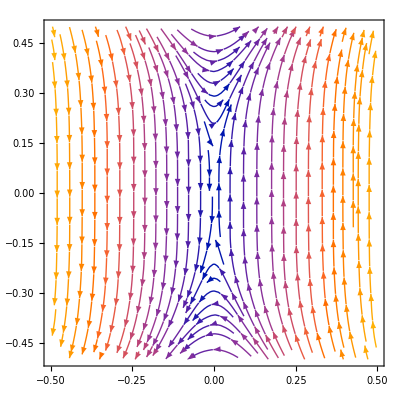

```mathematica
ClearAll["Global'.*"];
eq1 = y^3;
eq2 = x;

StreamPlot[{eq1, eq2}, {x, -0.5, 0.5}, {y, -0.5, 0.5}, StreamPoints -> Fine]
```

## d) Give the index for the fixed point of

3

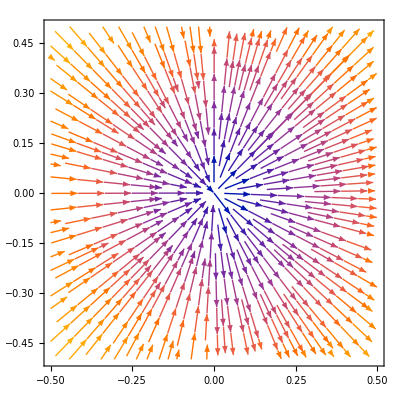

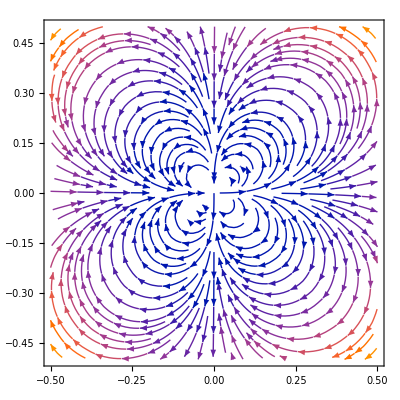

```mathematica
ClearAll["Global'.*"];
n = 1;
eq1 = (x^2 + y^2)^(Abs[n]/2)*Cos[n*ArcTan[y/x]];
eq2 = (x^2 + y^2)^(Abs[n]/2)*Sin[n*ArcTan[y/x]];

n = 3
eq3 = (x^2 + y^2)^(Abs[n]/2)*Cos[n*ArcTan[y/x]];
eq4 = (x^2 + y^2)^(Abs[n]/2)*Sin[n*ArcTan[y/x]];

StreamPlot[{eq1, eq2}, {x, -0.5, 0.5}, {y, -0.5, 0.5}, StreamPoints -> Fine]
StreamPlot[{eq3, eq4}, {x, -0.5, 0.5}, {y, -0.5, 0.5}, StreamPoints -> Fine]
```